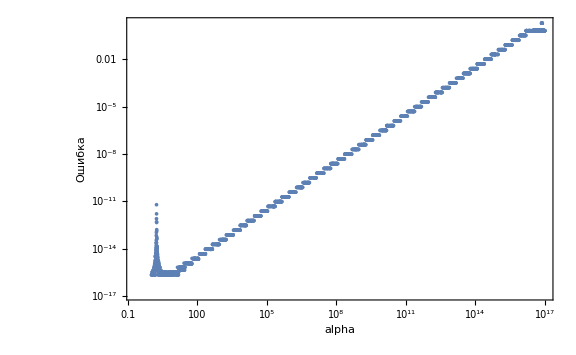

-Graphics-

```mathematica
ClearAll[cubeRoot, xTrue, alphas, dataAll, rootRe];cubeRoot[z_?NumericQ]:=Sign[z]*Abs[z]^(1/3);rootRe[alpha_?NumericQ]:=Module[{a=3.,b,c,p,q,s,y},b=alpha^2;c=3. alpha^2;p=b-a^2/3.;q=c-a b/3.+2 (a/3.)^3;s=Sqrt[(p/3.)^3+(q/2.)^2];y=cubeRoot[-q/2.+s]+cubeRoot[-q/2.-s];y-a/3.];

xTrue=-3.;
(*Так как x^3+3x^2+a^2x+3a^2=(x+3)(x^2+a^2)=0*)

alphas=10.^Subdivide[0,17,10000];
dataAll=Table[With[{x=rootRe[alpha]},{alpha,Abs[x/xTrue - 1]}],{alpha,alphas}];
ListLogLogPlot[
dataAll,
FrameLabel->{"alpha","Ошибка"},
Frame->True, 
ImageSize->Large, 
PlotRange->Automatic]
ListLogPlot[
dataAll,
FrameLabel->{"alpha","Ошибка"},
Frame->True, 
ImageSize->Large, 
PlotRange->Automatic]
```